# Mobius Transform

## it is a complex transform To show the transform can be viewed from 3-D

```mathematica
ω = (a+b z)/(c+d z) (* where a, b, c, d, z are complex *)
```

## On Polar Form

```mathematica
ω = (a ⅇ^(ⅈ α)+ b ⅇ^(ⅈ β) r ⅇ^(ⅈ θ))/(c ⅇ^(ⅈ γ)+ d ⅇ^(ⅈ δ) r ⅇ^(ⅈ θ))//Simplify
```

(a ⅇ^(ⅈ α)+b ⅇ^(ⅈ (β+θ)) r)/(c ⅇ^(ⅈ γ)+d ⅇ^(ⅈ (δ+θ)) r)

## a simple form (1-z)/(1+ z)

```mathematica
ω =(1- x - y ⅈ)/(1+x+y ⅈ)
```

```mathematica
ComplexExpand [(a-x-ⅈ y)/(b+x+ⅈ y)]
```

(a b)/((b+x)^2+y^2)+(a x)/((b+x)^2+y^2)-(b x)/((b+x)^2+y^2)-x^2/((b+x)^2+y^2)-y^2/((b+x)^2+y^2)+ⅈ (-(a y)/((b+x)^2+y^2)-(b y)/((b+x)^2+y^2))

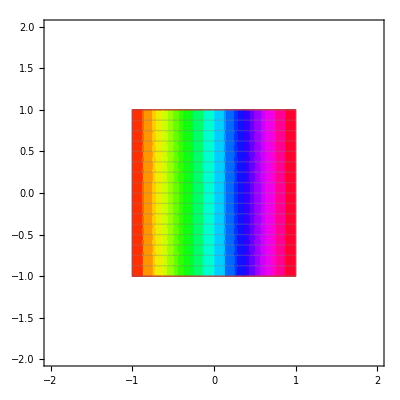

```mathematica
ParametricPlot[{x,y},{x,-1,1},{y,-1,1},PlotRange->{{-2,2},{-2,2}},ColorFunction->Function[{x,y,u},Hue[u]]]
```

```mathematica
Manipulate[ParametricPlot[{(a b)/((b+x)^2+y^2)+(a x)/((b+x)^2+y^2)-(b x)/((b+x)^2+y^2)-x^2/((b+x)^2+y^2)-y^2/((b+x)^2+y^2),(-(a y)/((b+x)^2+y^2)-(b y)/((b+x)^2+y^2))},{x,-1,1},{y,-1,1},PlotRange->{{-2,2},{-2,2}},ColorFunction->Function[{x,y,u},Hue[u]]],{a,-3,3},{b,-3,3}]
```

```mathematica
ComplexExpand[ (1-x-ⅈ y)/(1+x+ⅈ y)]
```

1/((1+x)^2+y^2)-x^2/((1+x)^2+y^2)-(2 ⅈ y)/((1+x)^2+y^2)-y^2/((1+x)^2+y^2)

```mathematica
Solve[{1/((1+x)^2+y^2)-x^2/((1+x)^2+y^2)-y^2/((1+x)^2+y^2)==h,-(2  y)/((1+x)^2+y^2)==k},{x,y}]
```

{{y→-(2 k)/(1+2 h+h^2+k^2),x→(1-h^2-k^2)/(1+2 h+h^2+k^2)}}

```mathematica
Simplify[((1-h^2-k^2)/(1+2 h+h^2+k^2))^2+(-(2 k)/(1+2 h+h^2+k^2))^2==r^2]
```

(1-2 h+h^2+k^2)/(1+2 h+h^2+k^2)==r^2

```mathematica
Collect[1-2 h+h^2+k^2-r^2(1+2 h+h^2+k^2)==0,{h,k}]
```

1-r^2+h (-2-2 r^2)+h^2 (1-r^2)+k^2 (1-r^2)==0

```mathematica
Collect[m(1-h^2-k^2)+c(1+2 h+h^2+k^2)==(-2 k),{h,k}]
```

c+2 c h+h^2 (c-m)+k^2 (c-m)+m==-2 k